## Lindblad方程

考虑动力学方程
-Graphics-
取L = σx, σy, σz, 利用NDSolve求解密度矩阵的演化：

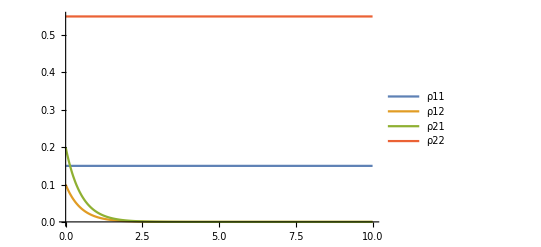

```mathematica
Clear["Global`*"];
γ1=0.0;γ2=0.0;γ3=0.5;ω=0.00;
σx=PauliMatrix[1];
σy=PauliMatrix[2];
σz=PauliMatrix[3];
σ1={{0,1},{0,0}};
σ2={{0,0},{1,0}};
ρ={{ρ11[t],ρ12[t]},{ρ21[t],ρ22[t]}};
L1=σx;
L2=σy;
L3=σz;
L=-I*ω(σz.ρ-ρ.σz)+γ1(2L1.ρ.Conjugate@Transpose[L1]-ρ.Conjugate@Transpose[L1].L1-Conjugate@Transpose[L1].L1.ρ)+γ2(2L2.ρ.Conjugate@Transpose[L2]-ρ.Conjugate@Transpose[L2].L2-Conjugate@Transpose[L2].L2.ρ)+γ3(2L3.ρ.Conjugate@Transpose[L3]-ρ.Conjugate@Transpose[L3].L3-Conjugate@Transpose[L3].L3.ρ);
s=NDSolve[{D[ρ,t]==L,ρ11[0]==0.15,ρ12[0]==0.1,ρ21[0]==0.2,ρ22[0]==0.55},{ρ11[t],ρ12[t],ρ21[t],ρ22[t]},{t,0,100}];
Plot[{ρ11[t]/.s,ρ12[t]/.s,ρ21[t]/.s,ρ22[t]/.s},{t,0,10},PlotLegends->{"ρ11","ρ12","ρ21","ρ22"}]
```

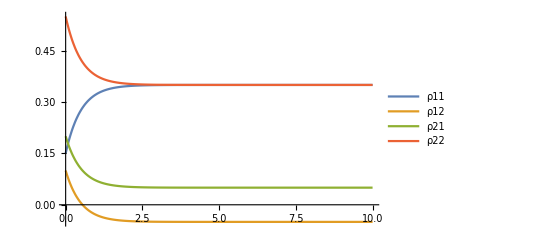

```mathematica
Clear["Global`*"];
γ1=0.0;γ2=0.5;γ3=0.0;ω=0.00;
σx=PauliMatrix[1];
σy=PauliMatrix[2];
σz=PauliMatrix[3];
σ1={{0,1},{0,0}};
σ2={{0,0},{1,0}};
ρ={{ρ11[t],ρ12[t]},{ρ21[t],ρ22[t]}};
L1=σx;
L2=σy;
L3=σz;
L=-I*ω(σz.ρ-ρ.σz)+γ1(2L1.ρ.Conjugate@Transpose[L1]-ρ.Conjugate@Transpose[L1].L1-Conjugate@Transpose[L1].L1.ρ)+γ2(2L2.ρ.Conjugate@Transpose[L2]-ρ.Conjugate@Transpose[L2].L2-Conjugate@Transpose[L2].L2.ρ)+γ3(2L3.ρ.Conjugate@Transpose[L3]-ρ.Conjugate@Transpose[L3].L3-Conjugate@Transpose[L3].L3.ρ);
s=NDSolve[{D[ρ,t]==L,ρ11[0]==0.15,ρ12[0]==0.1,ρ21[0]==0.2,ρ22[0]==0.55},{ρ11[t],ρ12[t],ρ21[t],ρ22[t]},{t,0,100}];
Plot[{ρ11[t]/.s,ρ12[t]/.s,ρ21[t]/.s,ρ22[t]/.s},{t,0,10},PlotLegends->{"ρ11","ρ12","ρ21","ρ22"}]
```